```mathematica
(* Use NDSolve to solve the Friedmann equation for a[t] *)

(* first case k=1 lambda =3, m=0,C=0 *)

ode1={a'[t]-√(1+a[t]^2)==0,a[0]==1};
```

```mathematica
sol=NDSolve[ode1,a,{t,0,10}]
```

{{a→InterpolatingFunction[…]}}

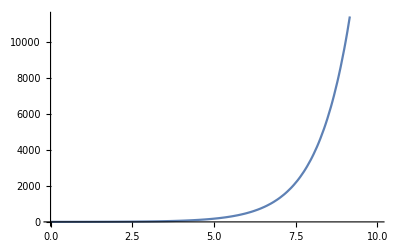

```mathematica
Plot[a[t]/.sol,{t,0,10}]
```

```mathematica
(* second case k=0, Lambda = .15, m=1, C=0 *)

ode1={a'[t]-√(1/a[t]+.05 a[t]^2)==0,a[0]==.0000001};
```

```mathematica
sol=NDSolve[ode1,a,{t,0,10}]
```

{{a→InterpolatingFunction[…]}}

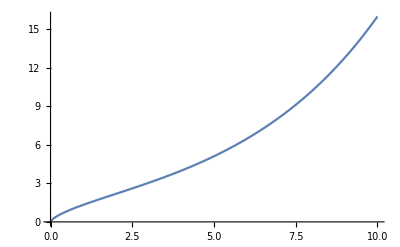

```mathematica
Plot[a[t]/.sol,{t,0,10}]
```

```mathematica
(* third case k=0, Lambda = .15, m=0, C=1 *)
```

```mathematica
ode1={a'[t]-√(1/a[t]^2+.05 a[t]^2)==0,a[0]==.0000001};
```

```mathematica
sol=NDSolve[ode1,a,{t,0,10}]
```

{{a→InterpolatingFunction[…]}}

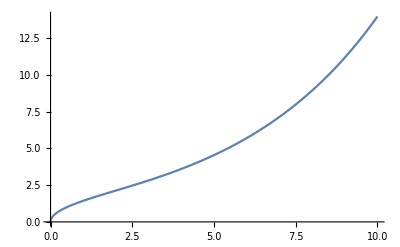

```mathematica
Plot[a[t]/.sol,{t,0,10}]
```

```mathematica
(* Fouth case k=0, Lambda = .15, m=1, C=1 *)

ode1={a'[t]-√(1/a[t]+1/a[t]^2+.05 a[t]^2)==0,a[0]==.0000001};
```

```mathematica
sol=NDSolve[ode1,a,{t,0,10}]
```

{{a→InterpolatingFunction[…]}}

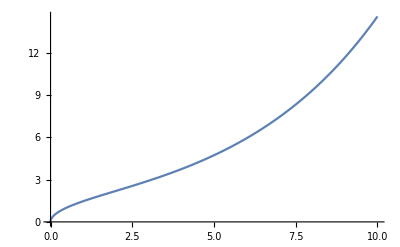

```mathematica
Plot[a[t]/.sol,{t,0,10}]
```